```mathematica
MatrixExp[-I*θ/4*l*PauliMatrix[3]].PauliMatrix[1].MatrixExp[I*θ/4*l*PauliMatrix[3]]/.{θ->0.1,l->1}
```

{{0,0.99875-0.0499792 ⅈ},{0.99875+0.0499792 ⅈ,0}}

```mathematica
MatrixExp[-I*θ/4*l*PauliMatrix[3]].MatrixExp[-I*θ/4*l*PauliMatrix[3]].PauliMatrix[1]
```

{{0,ⅇ^(-1/2 ⅈ l θ)},{ⅇ^((ⅈ l θ)/2),0}}

```mathematica
Cos[θ/2 l]PauliMatrix[1]+2Sin[θ/4 l]Cos[θ/4 l]PauliMatrix[2]/.{θ->0.1,l->1}
```

{{0,0.99875-0.0499792 ⅈ},{0.99875+0.0499792 ⅈ,0}}

```mathematica
MatrixExp[I*θ/4*l*PauliMatrix[3]]
```

{{ⅇ^((ⅈ l θ)/4),0},{0,ⅇ^(-1/4 ⅈ l θ)}}

```mathematica
PauliMatrix[0]*Cos[θ/4l]+I*PauliMatrix[3]Sin[θ/4l]//TrigToExp
```

{{ⅇ^((ⅈ l θ)/4),0},{0,ⅇ^(-1/4 ⅈ l θ)}}

```mathematica
PauliMatrix[3].PauliMatrix[1]
```

{{0,1},{-1,0}}

```mathematica
(Cos[θ/4 l]PauliMatrix[0]-I PauliMatrix[3]Sin[θ/4 l]).(Cos[θ/4 l]PauliMatrix[0]-I PauliMatrix[3]Sin[θ/4 l])//FullSimplify
```

{{ⅇ^(-1/2 ⅈ l θ),0},{0,ⅇ^((ⅈ l θ)/2)}}

```mathematica
PauliMatrix[3].PauliMatrix[2]-PauliMatrix[2].PauliMatrix[3]
```

{{0,-2 ⅈ},{-2 ⅈ,0}}

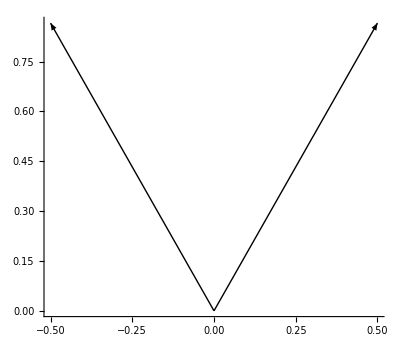

```mathematica
Graphics[{Arrow[{{0,0},{1/2,√3/2}}],Arrow[{{0,0},{-1/2,√3/2}}]},Axes->True]
```

```mathematica
RotationMatrix[-π/3].{0,1}
```

{(√3)/2,1/2}

```mathematica
f1=Import["fig1.gif"]
```

-Graphics-

```mathematica
d1=Import["D:\\CMTC\\TBG\\el.dat"];
```

```mathematica
Show[ListLinePlot[d1-2*^-3],f1]
```

-Graphics-

```mathematica
Rasterize@f1
```

-Graphics-

```mathematica
3n^2+3n+1/.n->Range[0,3]
```

{1,7,19,37}

```mathematica
3n^2+3n+1-(3n^2+3n+1/.n->n-1)//Simplify
```

6 n

```mathematica
RotationMatrix[0].{0,1}
```

{0,1}

```mathematica
shell[n_,a_]:=Block[{a1=a.{(√3)/2,1/2},a2=a.{-(√3)/2,1/2},list},list=Flatten[Table[{i,j},{i,-n,n},{j,Max[-n,i-n],Min[n,i+n]}],1];Transpose[{a1,a2}].#&/@list]
```

```mathematica
shell[1,RotationMatrix[0]]
```

{{-(√3)/2,-1/2},{0,-1},{-(√3)/2,1/2},{0,0},{(√3)/2,-1/2},{0,1},{(√3)/2,1/2}}

```mathematica
Flatten[(f[#1,#1]&/@{a,b,c})]
```

{f[a,a],f[b,b],f[c,c]}

```mathematica
Flatten[Outer[Plus,shell[2,1/4RotationMatrix[π/6]],shell[0,RotationMatrix[0]],1],1]
```

{{-1/4,-(√3)/4},{0,-(√3)/4},{1/4,-(√3)/4},{-3/8,-(√3)/8},{-1/8,-(√3)/8},{1/8,-(√3)/8},{3/8,-(√3)/8},{-1/2,0},{-1/4,0},{0,0},{1/4,0},{1/2,0},{-3/8,(√3)/8},{-1/8,(√3)/8},{1/8,(√3)/8},{3/8,(√3)/8},{-1/4,(√3)/4},{0,(√3)/4},{1/4,(√3)/4}}

```mathematica
shell[2,1/4RotationMatrix[π/6]]
```

{{-1/4,-(√3)/4},{0,-(√3)/4},{1/4,-(√3)/4},{-3/8,-(√3)/8},{-1/8,-(√3)/8},{1/8,-(√3)/8},{3/8,-(√3)/8},{-1/2,0},{-1/4,0},{0,0},{1/4,0},{1/2,0},{-3/8,(√3)/8},{-1/8,(√3)/8},{1/8,(√3)/8},{3/8,(√3)/8},{-1/4,(√3)/4},{0,(√3)/4},{1/4,(√3)/4}}

```mathematica
1/(√3)*RotationMatrix[π/6].{0,1}
```

{-1/(2 √3),1/2}

```mathematica
RotationMatrix[π/6].{0,1}
```

{-1/2,(√3)/2}

```mathematica
RotationMatrix[π/6].{1,0}*√3
```

{3/2,(√3)/2}

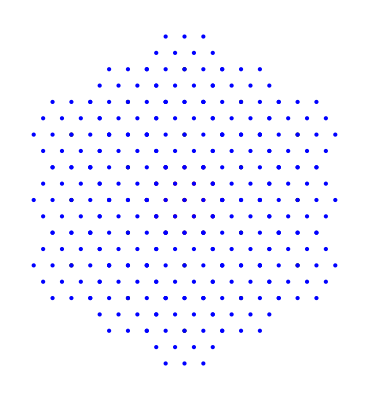

```mathematica
Graphics[{{Black,Point/@shell[2,RotationMatrix[0]]},{Red,Point/@shell[2,1/2*1/(√3)*RotationMatrix[π/6]]},{Blue,Point/@Flatten[Outer[Plus,shell[2,1/2*1/(√3)RotationMatrix[π/6]],shell[2,RotationMatrix[0]],1],1]}}]
```

```mathematica
{{a1x,a2x},{a1y,a2y}}.{i,j}
```

{a1x i+a2x j,a1y i+a2y j}

```mathematica
b1=4 π/(√3 am)*{1/2,(√3)/2,0}
```

{(2 π)/(√3 am),(2 π)/am,0}

```mathematica
b2=4 π/(√3 am)*{-1/2,(√3)/2,0}
```

{-(2 π)/(√3 am),(2 π)/am,0}

```mathematica
b3=2 π/am*{0,0,1}
```

{0,0,(2 π)/am}

```mathematica
2π*Inverse[{b1,b2,b3}]//MatrixForm
```

((√3 am)/2 | -(√3 am)/2 | 0
am/2 | am/2 | 0
0 | 0 | am)

```mathematica
kx=Import[NotebookDirectory[]<>"kx.dat"];
```

```mathematica
ky=Import[NotebookDirectory[]<>"ky.dat"];
```

```mathematica
bc=Import[NotebookDirectory[]<>"berrycur.dat"];
```

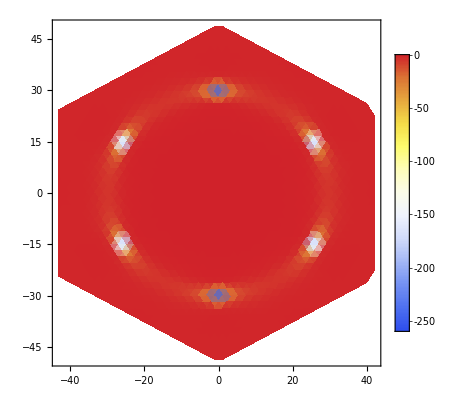

{{-42.571,0.,0.00126978},{-42.0321,0.933356,0.00126505},{-41.4932,1.86671,0.00126167},{-40.9544,2.80007,0.00125959},{-40.4155,3.73342,0.00125876},{-39.8766,4.66678,0.00125908},{-39.3377,5.60013,0.00126047},{-38.7989,6.53349,0.00126281},{-38.26,7.46685,0.00126596},{-37.7211,8.4002,0.00126978},{-37.1822,9.33356,0.0012741},{-36.6434,10.2669,0.00127874},6376,{36.6434,-10.2669,0.00127874},{37.1822,-9.33356,0.00127409},{37.7211,-8.4002,0.00126977},{38.26,-7.46685,0.00126596},{38.7989,-6.53349,0.00126281},{39.3377,-5.60013,0.00126047},{39.8766,-4.66678,0.00125908},{40.4155,-3.73342,0.00125875},{40.9544,-2.80007,0.00125959},{41.4932,-1.86671,0.00126167},{42.0321,-0.933356,0.00126505},{42.571,0.,0.00126978}}
 |  |  |  |

```mathematica
ListDensityPlot[Transpose@{Flatten@kx,Flatten@ky,1000Flatten@bc},ColorFunction->"TemperatureMap",PlotLegends->Automatic,PlotRange->Full]
```